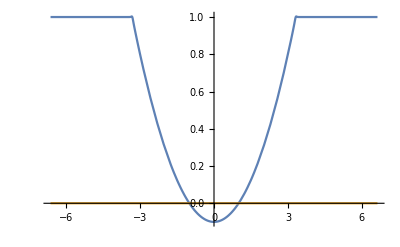

```mathematica
(*Configuration*)
a=0.1;
v=0.0000001;
n=100;

b=(1+1/a)^(-n);
Epsilon = Function[x,1+(a*(x^2-1)+ⅈ*v-1)/(1+b*x^(2n))];

X0=2*Sqrt[1/a+1];
Plot[{Re[Epsilon[x]],Im[Epsilon[x]]},{x,-X0,X0},PlotRange->Full]

χ=33;
A=1;
```

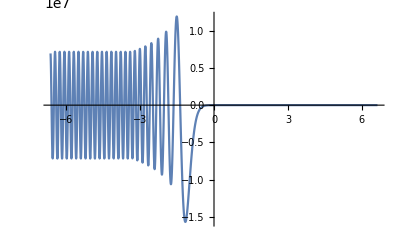

0.0382141

```mathematica
(*TE-wave*)
ETEEquation={y''[x]+χ^2*(Epsilon[x]-Sin[θ]^2)*y[x]==0};
ETEInitials={y[X0]==A,y'[X0]==ⅈ*χ*A};

ETE=ParametricNDSolveValue[{ETEEquation,ETEInitials},y,{x,-X0,X0},{θ}];
Plot[Re[ETE[0][x]],{x,-X0,X0},PlotRange->Full]

RTE=Function[θ,Exp[2*ⅈ*χ*(-X0)]*(ⅈ*χ*ETE[θ][-X0]-ETE[θ]'[-X0])/(ⅈ*χ*ETE[θ][-X0]+ETE[θ]'[-X0])];
TTE=Function[θ,ETE[θ][X0]*Exp[-ⅈ*χ*(X0)]*(Exp[ⅈ*χ*(-X0)]+RTE[θ]*Exp[-ⅈ*χ*(-X0)])/ETE[θ][-X0]];

TEDissipation =Function[θ,1 - Abs[RTE[θ]]^2-Abs[TTE[θ]]^2];
TEDissipation[0]
(*Plot[TEDissipation[θ],{θ,-π/2,π/2},PlotRange->Full]*)
```

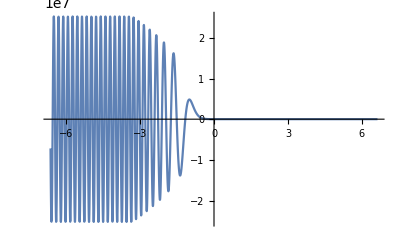

0.0000389208

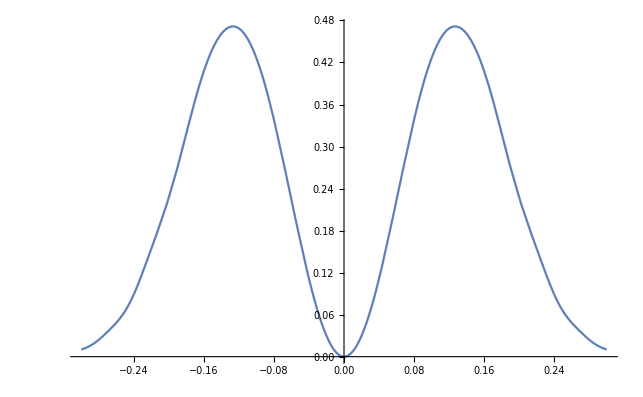

```mathematica
(*TM-wave*)
BTMEquation={y''[x]-(Epsilon'[x]/Epsilon[x])*y'[x]+χ^2*(Epsilon[x]-Sin[θ]^2)*y[x]==0};
BTMInitials={y[X0]==-A,y'[X0]==-ⅈ*χ*Epsilon[X0]*A*Cos[θ]};

BTM=ParametricNDSolveValue[{BTMEquation,BTMInitials},y,{x,-X0,X0},{θ}];
Plot[Re[BTM[0][x]],{x,-X0,X0},PlotRange->Full]

RTM=Function[θ,Exp[2*ⅈ*χ*(-X0)]*(ⅈ*χ*BTM[θ][-X0]-BTM[θ]'[-X0])/(ⅈ*χ*BTM[θ][-X0]+BTM[θ]'[-X0])];
TTM=Function[θ,BTM[θ][X0]*Exp[-ⅈ*χ*(X0)]*(Exp[ⅈ*χ*(-X0)]+RTM[θ]*Exp[-ⅈ*χ*(-X0)])/BTM[θ][-X0]];

TMDissipation=Function[θ,1-Abs[RTM[θ]]^2-Abs[TTM[θ]]^2];
TMDissipation[0]
Plot[TMDissipation[θ],{θ,-0.3,0.3},PlotRange->Full]
```

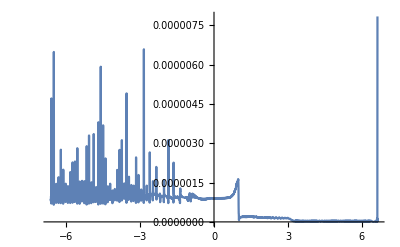

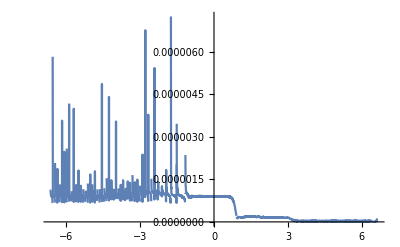

```mathematica
(*Reletive precision*)
ETM=Function[x,ⅈ*BTM[0]'[x]/(χ*Epsilon[x])];
Plot[Abs[ETE[0][x]-ETM[x]]/Min[Abs[ETE[0][x]],Abs[ETM[x]]],{x,-X0,X0},PlotRange->Full]

BTE=Function[x,(-ⅈ/χ)*ETE[0]'[x]];
Plot[Abs[BTE[x]+BTM[0][x]]/Min[Abs[BTE[x]],Abs[BTM[0][x]]],{x,-X0,X0},PlotRange->Full]
```